#### Init

```mathematica
matall = CloudImport[["https://www.wolframcloud.com/obj/e7ebcbbe-efed-4c19-850c-b8df05128b0c"](https://www.wolframcloud.com/obj/e7ebcbbe-efed-4c19-850c-b8df05128b0c)];
```

```mathematica
diffs = DeleteCases[Position[matall,1],{x_,x_}];
```

### All matrix

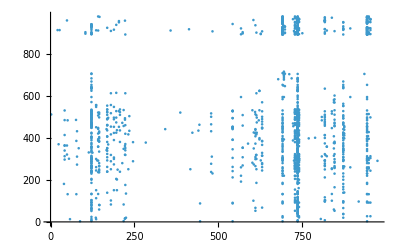

```mathematica
ListPlot[diffs]
```

### All by rank

```mathematica
aps=Select[Catenate[Values[$LifeParts[#]]&/@Keys[$LifeParts]],Length[#]<300&&Times@@Dimensions[#[[-1]]]<=1000&];
```

```mathematica
top2 = CellularAutomatonHistoryPlot["GameOfLife", {#[[-1]], 0}, Length[#]]&/@aps[[TakeLargestBy[Range[Length[matall]], Total[matall[[#]]]&, 20]]];
```

```mathematica
With[{tots = ReverseSort[Total/@ matall]},
ListLogLogPlot[ReplacePart[tots/Total[tots],Table[i-> Callout[tots[[i]]/Total[tots], top2[[i]]], {i, 1, 20}]], Frame-> True, FrameLabel->{"rank", "frequency"} ]
 ]
```

-Graphics-

### We need to associate elements in $LifeParts with $LifeData ... e.g. so we can plot frequency of use vs. year

```mathematica
Select[<|a->1|>, # === 1&]
```

<|a→1|>

```mathematica
names = Keys[Select[Join@@($LifeParts[#]&/@Keys[$LifeParts]), Length[#]<300&&Times@@Dimensions[#[[-1]]]<=1000&]];
```

```mathematica
usednames = names[[Catenate[Position[matall[[#]], 1]]]]&/@TakeLargestBy[Range[Length[matall]], Total[matall[[#]]]&, 20];
```

```mathematica
usednames
```

$Aborted

```mathematica
BubbleChart[
(KeyValueMap[Append[#1, #2]&, #]&/@ Counts/@(Sort/@ MapIndexed[{$LifeData[#]["Year"], First[#2]}&, usednames, {2}])), FrameTicks-> {{Transpose[{Range[20], names[[TakeLargestBy[Range[Length[matall]], Total[matall[[#]]]&, 20]]]}], Automatic}, {Automatic, Automatic}}, PlotLabel->"Usage over time", LabelingFunction->None
]
```

-Graphics-

### What fraction of patterns are elements of old patterns?

```mathematica
matalldiff = ReplacePart[matall, Thread[Table[{i, i}, {i, Length[matall]}]-> 0]];
```

#### V1

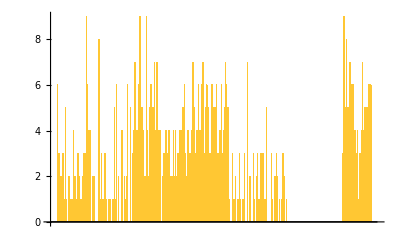

```mathematica
BarChart[Total/@Transpose[matalldiff]]
```

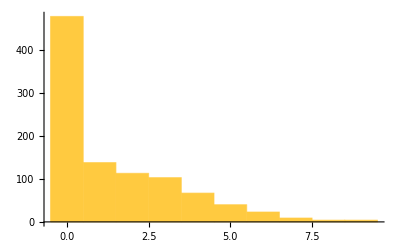

```mathematica
Histogram[Total/@Transpose[matalldiff]]
```

Over number of parts

Just number of parts

```mathematica
Length[aps]
```

979

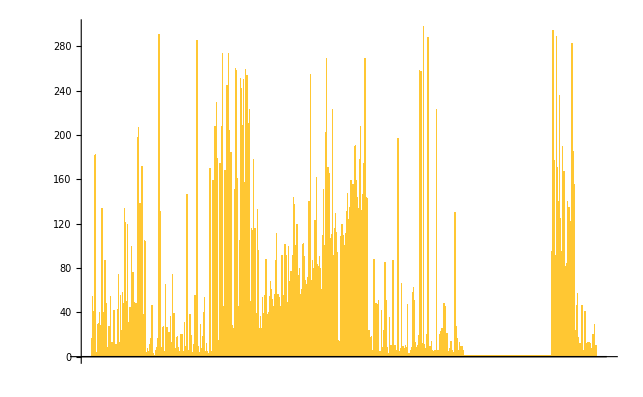

```mathematica
BarChart[Length/@aps, PlotRange->All]
```

Is that still lives?

```mathematica
ls = Map[Values[Length/@#]&, $LifeParts];
```

```mathematica
KeySortBy[<|b-> 1, a-> 2|>, #&]
```

<|a→2,b→1|>

```mathematica
bytime = (KeyValueMap[If[600>#2>400, Callout[#2, $LifeData[#1]["Year"],Top],#2]&, KeySortBy[#, $LifeData[#]["Year"]&]]&/@Map[Length, $LifeParts, {2}]);
```

```mathematica
cos =
((KeyValueMap[If[400>#2>300, Callout[#2, $LifeData[#1]["Year"],Top],#2]&, #]&)/@Map[Length, $LifeParts, {2}]);
```

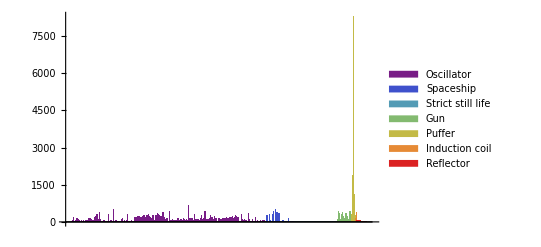

```mathematica
BarChart[ls, PlotRange->500, ChartStyle->{"Rainbow", None}, ChartLegends->Automatic]
```

```mathematica
BarChart[bytime, PlotRange->600, ChartStyle->{"Rainbow", None}, ChartLegends->Automatic, Frame->True, FrameLabel->{None, "unique parts"}]
```

-Graphics-

```mathematica
BarChart[cos, PlotRange->600, ChartStyle->{"Rainbow", None}, ChartLegends->Automatic]
```

-Graphics-

```mathematica
BarChart[Map[Length, $LifeParts, {2}]]
```

$Aborted

```mathematica
Length/@ $LifeParts
```

<|Oscillator→768,Spaceship→110,Strict still life→169,Gun→53,Puffer→16,Induction coil→7,Reflector→38|>

```mathematica
Map[ArrayPlot[#, ImageSize->20]&, Select[aps, Length[#] <=1&], {2}]
```

{{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-}}

Used / total

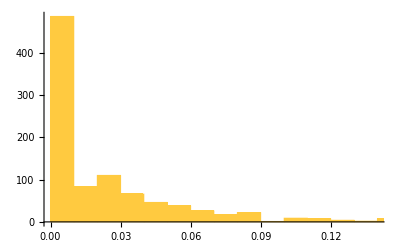

```mathematica
With[{tots = Total/@Transpose[matalldiff]},
Histogram[Table[tots[[i]]/Length[aps[[i]]],{i,  Range[Length[tots]]}]]
]
```

```mathematica
With[{tots = Total/@Transpose[matalldiff]},
Histogram[Table[tots[[i]]/Length[aps[[i]]],{i,  Range[Length[tots]]}]]
]
```

#### V2

Number of unique parts sorted by time grouped by class

```mathematica
bytime = (KeyValueMap[If[600>#2>400, Callout[#2, $LifeData[#1]["Year"],Top],#2]&, KeySortBy[#, $LifeData[#]["Year"]&]]&/@Map[Length, $LifeParts, {2}]);
```

```mathematica
BarChart[bytime, PlotRange->600, ChartStyle->{"Rainbow", None}, ChartLegends->Automatic, Frame->True, FrameLabel->{None, "unique parts"}]
```

-Graphics-

Number of unique dependent parts

```mathematica
Length/@ $LifeParts
```

<|Oscillator→768,Spaceship→110,Strict still life→169,Gun→53,Puffer→16,Induction coil→7,Reflector→38|>

```mathematica
$LifeParts[[1]][[idxs[[1]]]]]
```

636

```mathematica
Length/@idxs
```

{636,86,169,37,8,6,37}

```mathematica
small = MapThread[#1[[#2]]&, {Values[$LifeParts], idxs}];
```

```mathematica
idxsbytime = Function[parts, SortBy[Range[Length[parts]],$LifeData[Keys[parts][[#]]]["Year"]&]]/@ small;
```

```mathematica
smallbytime = MapThread[#1[[#2]]&, {small, idxsbytime}];
```

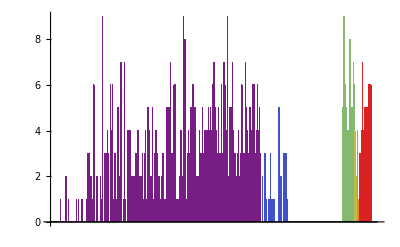

```mathematica
With[{tots = Total/@Transpose[matalldiff]}, BarChart[MapThread[#1[[#2]]&, {TakeList[tots, Length/@ small], idxsbytime}], ChartStyle->{"Rainbow", None}]]
```

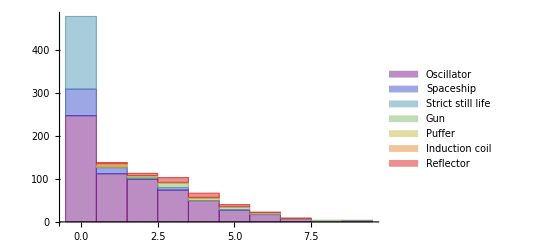

```mathematica
With[{tots = Total/@Transpose[matalldiff]}, Histogram[MapThread[#1[[#2]]&, {TakeList[tots, Length/@ small], idxsbytime}], ChartLayout->"Stacked",ChartLegends->Keys[$LifeParts], ChartStyle->"Rainbow"]]
```

```mathematica
Histogram[Total/@Transpose[matalldiff]]
```

-Graphics-

number of unique dependent parts over number of unique parts

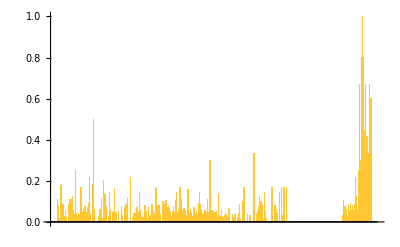

```mathematica
With[{tots = Total/@Transpose[matalldiff]},
BarChart[Table[tots[[i]]/Length[aps[[i]]],{i,  Range[Length[tots]]}]]
]
```

Grouped and sorted by time

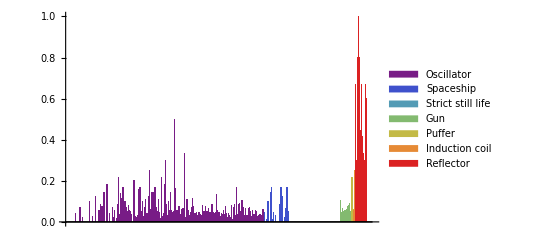

```mathematica
With[{tots = Total/@Transpose[matalldiff]},
BarChart[AssociationThread[ Keys[$LifeParts]->(MapThread[#1[[#2]]&, {TakeList[tots, Length/@ small], idxsbytime}] / Map[Values[Length/@#]&, smallbytime])], ChartStyle->{"Rainbow", None}, ChartLegends-> Automatic]
]
```

### Highlight uses of object in e.g.: -Graphics-

```mathematica
aps[[TakeLargestBy[Range[Length[matall]], Total[matall[[#]]]&, 20][[9]]]][[-1]]
```

```mathematica
Length[names]
```

979

```mathematica
names[[TakeLargestBy[Range[Length[matall]], Total[matall[[#]]]&, 20][[9]]]]
```

{{{0,0,0,0,1,1},{0,0,1,0,1,1},{0,1,0,0,0,0},{0,0,0,0,1,0},{1,1,0,1,0,0},{1,1,0,0,0,0}},{{0,0,0,1,1,1},{0,0,0,1,1,1},{0,0,0,1,1,1},{1,1,1,0,0,0},{1,1,1,0,0,0},{1,1,1,0,0,0}},{{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0},{0,0,0,1,1,1,0,1},{0,0,1,0,1,1,0,0},{0,0,1,1,0,1,0,0},{1,0,1,1,1,0,0,0},{0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0}},{{0,0,0,0,0,1,0,0},{0,0,0,0,1,0,1,0},{0,0,0,1,0,0,0,1},{0,0,1,0,0,0,1,0},{0,1,0,0,0,1,0,0},{1,0,0,0,1,0,0,0},{0,1,0,1,0,0,0,0},{0,0,1,0,0,0,0,0}},{{0,0,0,0,0,1,0,0},{0,0,0,0,1,1,1,0},{0,0,0,1,0,1,1,1},{0,0,1,0,0,0,1,0},{0,1,0,0,0,1,0,0},{1,1,1,0,1,0,0,0},{0,1,1,1,0,0,0,0},{0,0,1,0,0,0,0,0}},{{0,0,0,0,1,1,1,0},{0,0,0,0,0,0,0,1},{0,0,0,1,0,0,0,1},{0,0,1,0,1,0,0,1},{1,0,0,1,0,1,0,0},{1,0,0,0,1,0,0,0},{1,0,0,0,0,0,0,0},{0,1,1,1,0,0,0,0}},{{0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,1,1,0,0},{0,0,0,0,0,1,1,0,1,0},{0,0,0,0,1,0,0,1,1,1},{0,0,0,1,0,1,0,1,0,0},{0,0,1,0,1,0,1,0,0,0},{1,1,1,0,0,1,0,0,0,0},{0,1,0,1,1,0,0,0,0,0},{0,0,1,1,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0}},{{0,0,0,0,0,0,1,1,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,1},{0,0,0,0,1,0,0,0,0,1},{0,0,0,1,0,1,0,1,0,0},{0,0,1,0,1,0,1,0,0,0},{1,0,0,0,0,1,0,0,0,0},{1,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,1,1,0,0,0,0,0,0}}}

```mathematica
frames = 
CellularAutomaton["GameOfLife", {aps[[TakeLargestBy[Range[Length[matall]], Total[matall[[#]]]&, 20][[9]]]][[-1]], 0}, ]
```

{{0,0,0,0,0,0,1,1,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,1},{0,0,0,0,1,0,0,0,0,1},{0,0,0,1,0,1,0,1,0,0},{0,0,1,0,1,0,1,0,0,0},{1,0,0,0,0,1,0,0,0,0},{1,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,1,1,0,0,0,0,0,0}}

```mathematica
CausalSeparation[]
```

```mathematica
CellularAutomaton["GameOfLife", {#MatrixData, 0}, #Period]&[$LifeData[names[[TakeLargestBy[Range[Length[matall]], Total[matall[[#]]]&, 20][[9]]]]]]
```

{{{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,1,1,0,0,0,0,0,0},{0,0,1,1,0,1,0,0,0,0},{0,0,0,0,0,0,1,0,0,0},{0,0,0,1,0,0,0,0,0,0},{0,0,0,0,1,0,1,1,0,0},{0,0,0,0,0,0,1,1,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,1,1,1,0,0,0,0,0},{0,0,1,1,1,0,0,0,0,0},{0,0,1,1,1,0,0,0,0,0},{0,0,0,0,0,1,1,1,0,0},{0,0,0,0,0,1,1,1,0,0},{0,0,0,0,0,1,1,1,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0},{0,0,1,0,1,0,0,0,0,0},{0,1,0,0,0,1,0,0,0,0},{0,0,1,0,0,0,1,0,0,0},{0,0,0,1,0,0,0,1,0,0},{0,0,0,0,1,0,0,0,1,0},{0,0,0,0,0,1,0,1,0,0},{0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0},{0,0,1,1,1,0,0,0,0,0},{0,1,1,1,0,1,0,0,0,0},{0,0,1,0,0,0,1,0,0,0},{0,0,0,1,0,0,0,1,0,0},{0,0,0,0,1,0,1,1,1,0},{0,0,0,0,0,1,1,1,0,0},{0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0,0,0},{0,0,1,1,1,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0},{0,1,0,0,0,1,0,0,0,0},{0,1,0,0,1,0,1,0,0,0},{0,0,0,1,0,1,0,0,1,0},{0,0,0,0,1,0,0,0,1,0},{0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,1,1,1,0,0},{0,0,0,0,0,0,0,0,0,0}},{{0,0,0,1,0,0,0,0,0,0},{0,0,1,1,0,0,0,0,0,0},{0,1,0,1,1,0,0,0,0,0},{1,1,1,0,0,1,0,0,0,0},{0,0,1,0,1,0,1,0,0,0},{0,0,0,1,0,1,0,1,0,0},{0,0,0,0,1,0,0,1,1,1},{0,0,0,0,0,1,1,0,1,0},{0,0,0,0,0,0,1,1,0,0},{0,0,0,0,0,0,1,0,0,0}},{{0,0,1,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{1,0,0,0,1,0,0,0,0,0},{1,0,0,0,0,1,0,0,0,0},{0,0,1,0,1,0,1,0,0,0},{0,0,0,1,0,1,0,1,0,0},{0,0,0,0,1,0,0,0,0,1},{0,0,0,0,0,1,0,0,0,1},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,1,0,0}},{{0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,1,0,1,1,1,0,0,0,0},{0,0,0,1,1,0,1,0,0,0},{0,0,0,1,0,1,1,0,0,0},{0,0,0,0,1,1,1,0,1,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,1,1,0,0,0,0,0,0},{0,0,1,1,0,1,0,0,0,0},{0,0,0,0,0,0,1,0,0,0},{0,0,0,1,0,0,0,0,0,0},{0,0,0,0,1,0,1,1,0,0},{0,0,0,0,0,0,1,1,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0}}}

```mathematica
aps[[TakeLargestBy[Range[Length[matall]], Total[matall[[#]]]&, 20]]]
```

```mathematica
Catenate[Position[mat[[TakeLargestBy[Range[Length[mat]], Total[mat[[#]]]&, 20][[2]]]], 1]]
```

```mathematica
MorphologicalComponents[]
```

```mathematica
Catenate[Position[matall[[TakeLargestBy[Range[Length[matall]], Total[matall[[#]]]&, 20][[9]]]], 1]]
```

{139,169,239,240,262,293,308,324,339,350,352,381,406,408,436,460,461,462,489,490,492,510,522,524,535,536,554,925}

```mathematica
ArrayPlot[SparseArray[#]]&/@
(Thread[#-> 1]&/@

CausalSeparation[SparseArray[(CellularAutomaton["GameOfLife", {#MatrixData, 0}, #Period]&[$LifeData[names[[139]]]])[[1]]]["NonzeroPositions"]])
```

```mathematica
(Transpose[Reverse@{#[[All, 1]] -  Min[#[[All, 1]]]+1, #[[All, 2]] -  Min[#[[All, 2]]]+1}]&[
Ramp[#[[-1]] ]]+ 1)&[
CausalSeparation[SparseArray[(CellularAutomaton["GameOfLife", {#MatrixData, 0}, #Period]&[$LifeData[names[[139]]]])[[1]]]["NonzeroPositions"]][[1]]
]
```

Part::partd: Part specification {15,4}⟦All,1⟧ is longer than depth of object.

Part::partd: Part specification {15,4}⟦All,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{2,2}

```mathematica
ArrayPlot[SparseArray[Thread[(9-  (Transpose[Reverse@{#[[All, 1]] -  Min[#[[All, 1]]]+1, #[[All, 2]] -  Min[#[[All, 2]]]+1}]&[
Ramp[#]])&[
CausalSeparation[SparseArray[(CellularAutomaton["GameOfLife", {#MatrixData, 0}, #Period]&[$LifeData[names[[139]]]])[[4]]]["NonzeroPositions"]][[1]]
])->1]]]
```

-Graphics-

```mathematica
9 - (Transpose[Reverse@{#[[All, 1]] -  Min[#[[All, 1]]]+1, #[[All, 2]] -  Min[#[[All, 2]]]+1}]&[
Ramp[#]])&[
CausalSeparation[SparseArray[(CellularAutomaton["GameOfLife", {#MatrixData, 0}, #Period]&[$LifeData[names[[139]]]])[[4]]]["NonzeroPositions"]][[1]]
] === (Transpose[Reverse@{#[[All, 1]] -  Min[#[[All, 1]]]+1, #[[All, 2]] -  Min[#[[All, 2]]]+1}]&[
Ramp[#]])&[
CausalSeparation[SparseArray[(CellularAutomaton["GameOfLife", {#MatrixData, 0}, #Period]&[$LifeData[names[[139]]]])[[4]]]["NonzeroPositions"]][[1]]
]
```

False

```mathematica
((Transpose[Reverse@{#[[All, 1]] -  Min[#[[All, 1]]]+1, #[[All, 2]] -  Min[#[[All, 2]]]+1}]&[
Ramp[#]])&/@
CausalSeparation[SparseArray[(CellularAutomaton["GameOfLife", {#MatrixData, 0}, #Period]&[$LifeData[names[[139]]]])[[1]]]["NonzeroPositions"]]
)
```

{{{5,1},{6,1},{3,2},{5,2},{6,2},{2,3},{5,4},{1,5},{2,5},{4,5},{1,6},{2,6}},{{5,1},{6,1},{7,1},{2,2},{5,2},{6,2},{7,2},{1,3},{3,3},{6,3},{7,3},{2,4}},{{1,1},{2,1},{1,2},{2,2}}}

```mathematica
MemberQ[
SparseArray[#]["NonzeroPositions"]&/@$LifeParts["Oscillator"]["Figure eight"], #
```

{{{1,5},{1,6},{2,3},{2,5},{2,6},{3,2},{4,5},{5,1},{5,2},{5,4},{6,1},{6,2}},{{1,4},{1,5},{1,6},{2,4},{2,5},{2,6},{3,4},{3,5},{3,6},{4,1},{4,2},{4,3},{5,1},{5,2},{5,3},{6,1},{6,2},{6,3}},{{1,6},{3,4},{3,5},{3,6},{3,8},{4,3},{4,5},{4,6},{5,3},{5,4},{5,6},{6,1},{6,3},{6,4},{6,5},{8,3}},{{1,6},{2,5},{2,7},{3,4},{3,8},{4,3},{4,7},{5,2},{5,6},{6,1},{6,5},{7,2},{7,4},{8,3}},{{1,6},{2,5},{2,6},{2,7},{3,4},{3,6},{3,7},{3,8},{4,3},{4,7},{5,2},{5,6},{6,1},{6,2},{6,3},{6,5},{7,2},{7,3},{7,4},{8,3}},{{1,5},{1,6},{1,7},{2,8},{3,4},{3,8},{4,3},{4,5},{4,8},{5,1},{5,4},{5,6},{6,1},{6,5},{7,1},{8,2},{8,3},{8,4}},{{1,7},{2,7},{2,8},{3,6},{3,7},{3,9},{4,5},{4,8},{4,9},{4,10},{5,4},{5,6},{5,8},{6,3},{6,5},{6,7},{7,1},{7,2},{7,3},{7,6},{8,2},{8,4},{8,5},{9,3},{9,4},{10,4}},{{1,7},{1,8},{3,6},{3,10},{4,5},{4,10},{5,4},{5,6},{5,8},{6,3},{6,5},{6,7},{7,1},{7,6},{8,1},{8,5},{10,3},{10,4}}}

```mathematica
CausalSeparation[SparseArray[(CellularAutomaton["GameOfLife", {#MatrixData, 0}, #Period]&[$LifeData[names[[139]]]])[[1]]]["NonzeroPositions"]]
```

{{{10,7},{10,8},{11,5},{11,7},{11,8},{12,4},{13,7},{14,3},{14,4},{14,6},{15,3},{15,4}},{{4,5},{4,6},{4,7},{5,2},{5,5},{5,6},{5,7},{6,1},{6,3},{6,6},{6,7},{7,2}},{{4,11},{4,12},{5,11},{5,12}}}

```mathematica
CausalSeparation[SparseArray[(CellularAutomaton["GameOfLife", {#MatrixData, 0}, #Period]&[$LifeData[names[[139]]]])[[1]]]["NonzeroPositions"]][[1]]
```

{{10,7},{10,8},{11,5},{11,7},{11,8},{12,4},{13,7},{14,3},{14,4},{14,6},{15,3},{15,4}}

```mathematica
Transpose[Reverse@{#[[All, 1]] -  Min[#[[All, 1]]]+1, #[[All, 2]] -  Min[#[[All, 2]]]+1}]
CausalSeparation[SparseArray[(CellularAutomaton["GameOfLife", {#MatrixData, 0}, #Period]&[$LifeData[names[[139]]]])[[1]]]["NonzeroPositions"]])
```

```mathematica
ArrayPad[SparseArray[
Thread[
(Transpose[Reverse@{#[[All, 1]] -  Min[#[[All, 1]]]+1, #[[All, 2]] -  Min[#[[All, 2]]]+1}]&[
Ramp[#[[-1]] ]]+ 1)->1]], {0, 1}]&[]
```

```mathematica
(*ArrayPad[SparseArray[
Thread[
(Transpose[Reverse@{#[[All, 1]] -  Min[#[[All, 1]]]+1, #[[All, 2]] -  Min[#[[All, 2]]]+1}]&[
Ramp[#[[-1]] ]]+ 1)->1]], {0, 1}]&/@*)
SparseArray/@(Thread[#-> 1]&/@CausalSeparation[SparseArray[(CellularAutomaton["GameOfLife", {#MatrixData, 0}, #Period]&[$LifeData[names[[139]]]])[[1]]]["NonzeroPositions"]])
```

{SparseArray[…],SparseArray[…],SparseArray[…]}

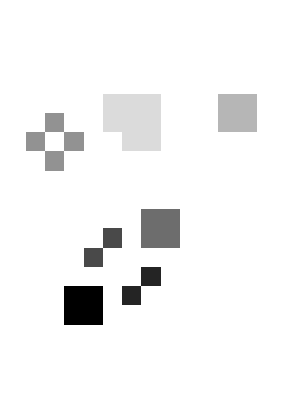

```mathematica
ArrayPlot[MorphologicalComponents@(CellularAutomaton["GameOfLife", {#MatrixData, 0}, #Period]&[$LifeData[names[[139]]]])[[1]]]
```

### How often are subpatterns reused within a single pattern (Relevant to invented or discovered)